```mathematica
$Assumptions={Element[{r,c, Ω},Reals],r>0,c>0, Ω > 0};

int = Integrate[1/Sqrt[u^2-r^2] Cos[Ω u/c], {u, r, Infinity}]
```

BesselJ[0,(r Ω)/c] Log[(2 c)/(r Ω)]-Hypergeometric0F1Regularized^(1,0)[1,-(r^2 Ω^2)/(4 c^2)]

```mathematica
int2  = Integrate[1/Sqrt[u^2-r^2] Sin[Ω u/c], {u, r, Infinity}]
```

1/2 π BesselJ[0,(r Ω)/c]

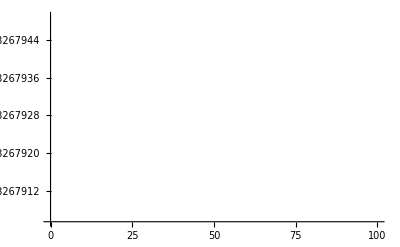

```mathematica
Plot[int2 /. {c-> 30000000, Ω -> 1}, {r, 0, 100}]
```

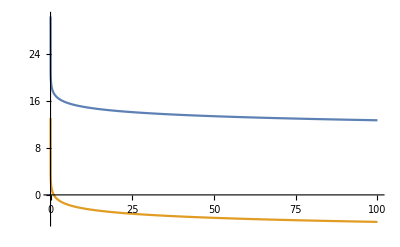

```mathematica
Plot[{int /. {c-> 30000000, Ω -> 1},- Log[r]}, {r, 0, 100}]
```

```mathematica
FullSimplify[Series[int Cos[Ω t]+int2 Sin[Ω t], {c,Infinity, 1}]]
```

1/2 (2 Cos[t Ω] Log[2]+2 Cos[t Ω] Log[c]-2 Cos[t Ω] Log[r]-2 Cos[t Ω] Log[Ω]+π Sin[t Ω]-2 Cos[t Ω] Hypergeometric0F1Regularized^(1,0)[1,0])+O[1/c]^2

```mathematica
prefactor = 1/4/π μ 2π I0 a^2/2 /(π a^2) 2 Ω
Eint =prefactor Integrate[1/Sqrt[u^2-r^2] Sin[Ω (t - u/c)], {u, r, Infinity}]
```

(I0 μ Ω)/(2 π)

1/(2 π)I0 μ Ω (-1/2 BesselJ[0,(r Ω)/c] (π Cos[t Ω]-2 Log[(2 c)/(r Ω)] Sin[t Ω])-Sin[t Ω] Hypergeometric0F1Regularized^(1,0)[1,-(r^2 Ω^2)/(4 c^2)])

```mathematica
FullSimplify[Series[Eint, {c, Infinity, 0}]]
```

-1/(4 π)I0 μ Ω (π Cos[t Ω]-2 Log[2] Sin[t Ω]-2 Log[c] Sin[t Ω]+2 Log[r] Sin[t Ω]+2 Log[Ω] Sin[t Ω]+2 Sin[t Ω] Hypergeometric0F1Regularized^(1,0)[1,0])+O[1/c]^1

```mathematica
FullSimplify[Series[int, {c,Infinity, 1}]]
```

(Log[2]+Log[c]-Log[r Ω]-Hypergeometric0F1Regularized^(1,0)[1,0])+O[1/c]^2

```mathematica
FullSimplify[Series[int2, {c,Infinity, 1}]]
```

π/2+O[1/c]^2

```mathematica
Derivative[1,0][Hypergeometric0F1Regularized][1,0]
```

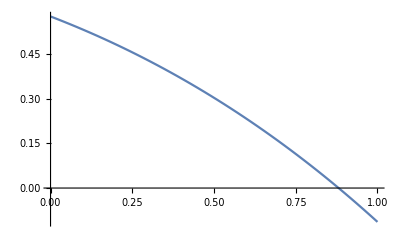

```mathematica
Plot[Derivative[1,0][Hypergeometric0F1Regularized][1,x], {x, 0,1}]
```